# Dataset preparation

```mathematica
ClearAll["Global`*"]
```

```mathematica
dataset=Import[FileNameJoin[{NotebookDirectory[], "dataset/dataset_full_2.wxf"}], "WXF"];
```

Global`FinishDynamic::shdw: Symbol FinishDynamic appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`CellEvaluationLanguage::shdw: Symbol CellEvaluationLanguage appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`LineColor::shdw: Symbol LineColor appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`OverTilde::shdw: Symbol OverTilde appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`LineOpacity::shdw: Symbol LineOpacity appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`Absolute::shdw: Symbol Absolute appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FrontFaceOpacity::shdw: Symbol FrontFaceOpacity appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`Projection::shdw: Symbol Projection appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`$InterfaceEnvironment::shdw: Symbol $InterfaceEnvironment appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`TemplateArgBox::shdw: Symbol TemplateArgBox appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`AllowKernelInitialization::shdw: Symbol AllowKernelInitialization appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`ConsoleMessage::shdw: Symbol ConsoleMessage appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`DeclareKnownSymbols::shdw: Symbol DeclareKnownSymbols appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`DisplayWith::shdw: Symbol DisplayWith appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`DisplayWithRef::shdw: Symbol DisplayWithRef appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`DisplayWithVariable::shdw: Symbol DisplayWithVariable appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`DrawEdges::shdw: Symbol DrawEdges appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`DrawFrontFaces::shdw: Symbol DrawFrontFaces appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`EdgeCapForm::shdw: Symbol EdgeCapForm appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`EdgeColor::shdw: Symbol EdgeColor appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`EdgeDashing::shdw: Symbol EdgeDashing appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`EdgeJoinForm::shdw: Symbol EdgeJoinForm appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`EdgeOpacity::shdw: Symbol EdgeOpacity appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`EdgeThickness::shdw: Symbol EdgeThickness appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FrontFaceColor::shdw: Symbol FrontFaceColor appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`GraphicsColor::shdw: Symbol GraphicsColor appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`GraphicsHighlightColor::shdw: Symbol GraphicsHighlightColor appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`NewPrimitiveStyle::shdw: Symbol NewPrimitiveStyle appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`RectangleBoxOptions::shdw: Symbol RectangleBoxOptions appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`RefBox::shdw: Symbol RefBox appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`SelectionDebuggerTag::shdw: Symbol SelectionDebuggerTag appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`UpdateDynamicObjects::shdw: Symbol UpdateDynamicObjects appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`UpdateDynamicObjectsSynchronous::shdw: Symbol UpdateDynamicObjectsSynchronous appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

## Statistics

Size of dataset

```mathematica
Length@dataset
```

285830

```mathematica
keyWords=Join@@(Cases[#, x_Symbol:>ToString[HoldForm@x],Infinity,Heads->True][[2;;-1]]&/@dataset[All,"code"])//Normal;
```

```mathematica
keyWords//InputForm
```

```mathematica
Length@keyWords
```

16725286

```mathematica
Counts[keyWords]
```

<|CompoundExpression→105565,Print→813,a→21976,Abort→124,b→13076,TimeConstrained→89,Pause→188,MemoryConstrained→14,Range→4438,Power→95632,79779,IPTCRaw→5,MakerNote→5,CopyMetaInformation→1,overwriteAllTags→2,inFPath→4,outFPath→4,GetXMP→1,tname→25,GetIPTC→1,GetExif→1|>
 |  |  |  |

```mathematica
expCounts=%49;
```

```mathematica
expCountsSorted=Sort[expCounts,Greater];
```

```mathematica
expCountsSortedDS=Dataset@expCountsSorted;
```

```mathematica
Length@expCountsSorted
```

79799

```mathematica
expCountsSortedFiltered=Sort[Association[(#-> expCountsSorted[#])&/@Names["System`*"]],Greater]
```

<|List→12543469,Rule→380749,Set→180779,Times→156783,CompoundExpression→105565,Null→101174,6578,$CloudExpressionBase→3,$SecuredAuthenticationKeyTokens→Missing[KeyAbsent,$SecuredAuthenticationKeyTokens],$Services→43,$SessionID→25,$ServiceCreditsAvailable→15,$SetParentLink→1|>
 |  |  |  |

```mathematica
ListLogPlot[expCountsSortedFiltered[[1;;5]],PlotRange->All,Filling->Bottom, PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
SpokenString[dataset[[1,"code"]]//Normal]
```

HoldComplete of the quantity print a semicolon abort semicolon print b

```mathematica
dataset
```

Dataset[<>]

## Label Extracting

```mathematica
(*tttt=Cases[dataset,_?(Function[code, Not@FreeQ[Unevaluated[code],$DATA$], HoldAllComplete])];*)
```

```mathematica
codeSetArray=dataset/.{
HoldComplete[(SetDelayed|Set)[(x_[___]|x_),y___]] :>{ToString[HoldForm[x]],HoldComplete[y]},
HoldComplete[CompoundExpression[(SetDelayed|Set)[(x_[___]|x_),y___],___]] :>{ToString[HoldForm[x]],HoldComplete[y]},
HoldComplete[y___]:> {Undefined,HoldComplete[y]}
};
```

```mathematica
codeSetArrayClean=Cases[codeSetArray,{_String,HoldComplete[___]},{1,2}];
```

```mathematica
codeSetArrayClean[[110]]//InputForm
```

{"f", HoldComplete[f[n - 1]]}

```mathematica
names=First[#]&/@codeSetArrayClean;
```

```mathematica
uniqNames=DeleteDuplicates[names];
```

```mathematica
uniqNames//Length
```

64936

```mathematica
Dataset@Sort[Counts[names],Greater]
```

$AutomaticUnitParsing::shdw: Symbol $AutomaticUnitParsing appears in multiple contexts {QuantityUnits`,Global`}; definitions in context QuantityUnits` may shadow or be shadowed by other definitions.

Dataset[<>]

## Tree form

```mathematica
names = AssociationMap[True &,Names["System`*"]];SetAttributes[expr2Str,HoldAllComplete];
expr2Str[expr_]:=First @ ReplaceAll[HoldComplete@expr,{
$DATA$:> RuleCondition["$DATA$"],
s:_Integer:>RuleCondition["$INT$"],
 s:_Real:>RuleCondition["$REAL$"], 
s:_String:>RuleCondition["$STR$"],
s:_Symbol/;names[ToString[Unevaluated[s]]]:>RuleCondition[SymbolName[Unevaluated[s]]],
s:_Symbol:>RuleCondition["$VAR$"]
}];

ClearAll[getGraph, igetGraph];
SetAttributes[processNode,HoldAll];
processNode[node_,nodes_]:=(nodes=Append[nodes,node];node)
Format[node[expr_, ___]]:=expr
igetGraph[expr_]:=(Increment[idx];Block[{content,head,id=idx},
content=(expr/.h_[a___]:>{h,{a}});
head=node[First[content], id];
Map[
Sow[UndirectedEdge[head,igetGraph[#]], "Edges"]&,Last[content]
];
head
]);
igetGraph[expr_]/;Depth[expr]==1:=(
id=PreIncrement[idx];
Sow[node[expr, id], "Nodes"]
);

getGraph[expr_] :=<|
"Nodes" -> {},
"Edges" -> {},
Last @ Reap[igetGraph[expr], _, Rule]
|>;

getDirection[h_,g_]:=(
ph=Table[Take[h,{i,i+1}],{i,Range[Length@h-1]}];
d=FreeQ[g,UndirectedEdge[#[[1]],#[[2]]]]&/@ph;
Thread[List[h,Append[d,Null]]]
);
SetAttributes[exprToPaths, HoldAllComplete]
SetAttributes[exprToGraph, HoldAllComplete]
exprToGraph[expr_] := Module[
{graph, paths},
idx=0;
graph = getGraph[expr2Str[expr]];
paths = Apply[
FindShortestPath[graph["Edges"],#1,#2]&,
Subsets[graph["Nodes"],{2}],
{1}
];
paths=Join[paths,FindShortestPath[graph["Edges"],graph["Edges"][[-1]][[1]],#]&/@graph["Nodes"]];
paths=Join[paths,If[Length@graph["Nodes"]==0,List@Cases[#, _String,Infinity,Heads->True],{}]]&@expr2Str[expr];
paths=DeleteDuplicates[paths];
<|
graph,
"Paths" -> paths,
"Directions" -> Map[getDirection[#, graph["Edges"]]&, paths]
|>
]

exprToPaths[expr_] := DeleteDuplicates[Flatten[#][[;;-2]]&/@(exprToGraph[expr]["Directions"]/.node[x_String,_]:>x)]
```

```mathematica
codeSetArrayCleanL[[7]][[2]]//FullForm
```

HoldComplete[DialogInput[CancelButton[]]]

```mathematica
(*fix problem with 7th*)
```

```mathematica
HoldComplete[DialogInput[CancelButton[]]]
```

```mathematica
data = exprToGraph@@codeSetArrayCleanL[[6]][[2]]
```

<|Nodes→{$STR$},Edges→{URL<->$STR$,LocalCache<->URL},Paths→{{LocalCache,URL,$STR$}},Directions→{{{LocalCache,False},{URL,False},{$STR$,Null}}}|>

```mathematica
exprToPaths@@codeSetArrayCleanL[[7]][[2]]
```

{{DialogInput,True,CancelButton}}

#### Apply

```mathematica
codeSetArrayCleanL=Select[codeSetArrayClean,Depth[#[[2]]]>3 &];
```

```mathematica
(*s=Sort[MapIndexed[{Depth@#1[[2]],#2}&,codeSetArrayCleanL],#1[[1]]>#2[[1]]&];*)
```

```mathematica
codeSetArrayCleanL[[1]][[2]]
```

HoldComplete[Module[{g=4 #1 (1-#1)&},x=TimeConstrained[Nest[g,1/10,n],1];If[x===$Aborted,x=Nest[g,0.1,n]];x]]

```mathematica
ddd=Sort[MapIndexed[{Length[Cases[expr2Str[#1[[2]]],"$VAR$"|"$INT$"|"$DATA$"|"$REAL$"|"$STR$",Infinity]],#2}&,codeSetArrayCleanL],#1[[1]]>#2[[1]]&];
```

```mathematica
ddd[[80000]]
```

{8,{126793}}

```mathematica
2^8
```

256

```mathematica
codeSetArrayCleanLC=Select[codeSetArrayCleanL,Length[Cases[expr2Str[#[[2]]],"$VAR$"|"$INT$"|"$DATA$"|"$REAL$"|"$STR$",Infinity]]≤9&];
```

```mathematica
codeSetArrayCleanLC//Length
```

84387

```mathematica
codeSetArrayCleanLC[[7]]//InputForm
```

{"cGen", HoldComplete[Block[{$CompilationTarget = "C"}, Compile[{{x}}, x^2 + Sin[x^2]]]]}

```mathematica
dataPredictor=Apply[
Function[{name, code}, {name, exprToPaths @@ code}], 
codeSetArrayCleanLC, 
{1}
];
```

```mathematica
dataPredictor//ByteCount
```

268357368

```mathematica
pathesDictData=Cases[dataPredictor,{l_,{x___}}:>x];
```

```mathematica
pathesDictData//Length
```

869339

```mathematica
DeleteDuplicates[pathesDictData]//Length
```

267480

```mathematica
pathesDictNames=Cases[dataPredictor,{l_,{x___}}:>l];
```

```mathematica
pathesDictNames//Length
```

84387

```mathematica
DeleteDuplicates[pathesDictNames]//Length
```

29925

```mathematica
dataPredictor=dataset;
```

```mathematica
dataPredictor=Select[dataPredictor,FreeQ[#,{}]&,Infinity];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "dataset/dataset_labels.wxf"}],dataPredictor,PerformanceGoal->"Size"]
```

/Users/ckorikov/___wss19/WSS-19/Final Project/Research/dataset/dataset_labels.wxf

```mathematica
c[n_]:=(n!)/(2!(n-2)!)
```

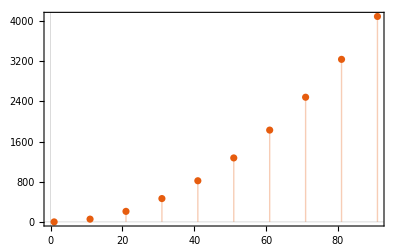

```mathematica
ListPlot[Map[{#,c[#]}&,Range[1,100,10]],PlotTheme->"Scientific",Filling->Bottom]
```

### Visualisation

```mathematica
data = exprToGraph[x^2+a(b+c^2)];
Animate[
Column@{
TreePlot[HighlightGraph[data[["Edges"]],data[["Paths", s]]],
Top,
data[["Edges", -1, 1]],
PlotTheme->"Minimal",VertexLabels->Automatic,ImageSize->Large],
data[["Directions", s]]
},
{s,1,Length@data["Directions"],1}
]
```

```mathematica
Export["test.gif",a,"GIF","AnimationRepetitions"->∞]
```

test.gif

## Token Sequence

### Lab

```mathematica
exp=dataset[[3]][["code"]]//Normal
```

HoldComplete[MemoryConstrained[Range[10^6],10000]]

```mathematica
{HoldComplete,MemoryConstrained,Range,Power, Intger, Integer}
```

```mathematica
heads = Cases[exp, _Symbol,Infinity,Heads->True]
```

{HoldComplete,MemoryConstrained,Range,Power}

```mathematica
Position[exp,Alternatives @@ heads]
```

{{0},{1,0},{1,1,0},{1,1,1,0}}

```mathematica
pos = Position[exp,MemoryConstrained]
```

{{1,0}}

```mathematica
Map[exp[[Sequence @@ #]]&,pos]
```

{MemoryConstrained}

```mathematica
Map[# -> Position[exp, #]&, heads]
```

{HoldComplete→{{0}},MemoryConstrained→{{1,0}},Range→{{1,1,0}},Power→{{1,1,1,0}}}

```mathematica
5
```

```mathematica
replaced = ReplaceAll[exp, s:_Integer|_Real|_String :> Block[{}, Type[Head[s], s] /; True]]
```

HoldComplete[MemoryConstrained[Range[Type[Integer,10]^Type[Integer,6]],Type[Integer,10000]]]

```mathematica
Cases[replaced, _Type, Infinity]
```

{Type[Integer],Type[Integer],Type[Integer]}

```mathematica
1.2//FullForm
```

1.2

### Extract

```mathematica
names = AssociationMap[True &,Names["System`*"]]; (*hash*)
ClearAll[getTokenSeq]
getTokenSeq[expr_]:=Rest @Flatten[
Last[
Reap[
 ReplaceAll[
expr,{
$DATA$:> RuleCondition[Sow@"$DATA$"],
s:_Integer:>RuleCondition[Sow@"$INT$"],
 s:_Real:>RuleCondition[Sow@"$REAL$"], 
s:_String:>RuleCondition[Sow@"$STR$"],
s:_Symbol/;names[ToString[Unevaluated[s]]]:>RuleCondition[Sow@SymbolName[Unevaluated[s]]],
s:_Symbol:>RuleCondition[Sow@"$VAR$"]
}
]
]
]
]
```

```mathematica
n=0;
ProgressIndicator[Dynamic[n],{1,Length[dataset]}]

tokens =  Map[
Function[n++;getTokenSeq[#]],
dataset
];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "dataset/dataset_token_sequence_2.wxf"}], tokens,"WXF"]
```

/Users/ckorikov/___wss19/WSS-19/Final Project/Research/dataset/dataset_token_sequence_2.wxf

```mathematica
Dataset@tokens
```

Dataset[<>]

## Paths Check

```mathematica
test=Import[FileNameJoin[{NotebookDirectory[], "dataset/dataset_token_sequence.wxf"}]];
```

{{CompoundExpression,Print,$VAR$,Abort,Print,$VAR$},{TimeConstrained,Pause,$INT$,$INT$},{MemoryConstrained,Range,Power,$INT$,$INT$,$INT$},285825,{End},{End}}
 |  |  |  |

```mathematica
Cases[test,{("Set"|"SetDelayed"),___}]//Length
```

70718